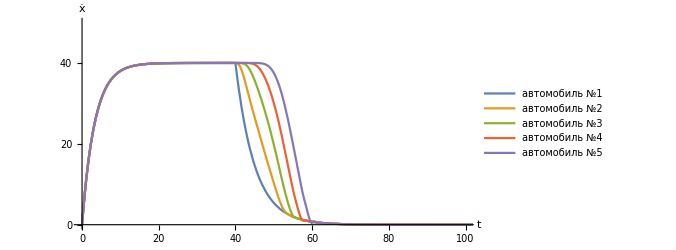

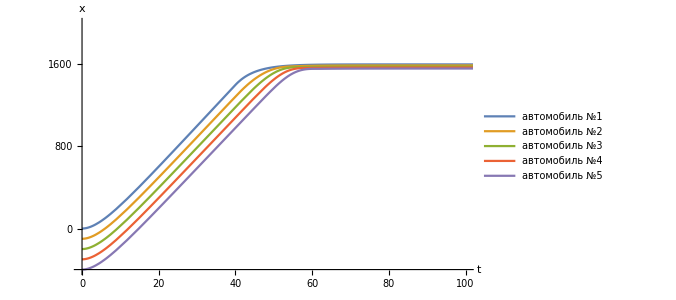

speed.pdf

path.pdf

```mathematica
speed =Module[{e},
tt=40;
tmax =150;
Subscript[V, max] =40;
vm=0;
τ = 1;

R[t_] := If[t <= tt, 1,0];
RR[t_] := If[t <= tt, 0,1];
λ=100;
T=0.1;
a=0.3;
q=0.2;
b=2;
Subscript[σ, 0]=10;
Subscript[σ, 1]=5;
Module[{},

solF= NDSolve[{u''[t]== R[t]* a *(Subscript[V, max]-u'[t])+RR[t]*q*(vm-u'[t]), u[t /; t≤ 0] == -0*λ, u'[t /; t≤ 0] == 0},u,{t,0 ,tmax}];
solS = NDSolve[{v''[t]==a*(Subscript[V, max]-v'[t])-q((Subscript[σ, 0]  +  (v'[t]*(v'[t]-Evaluate[u'[t-τ] /.solF][[1]])))/(Evaluate[u[t-τ] /.solF][[1]]-v[t]))^2, v[t /; t≤ τ ] == -1*λ, v'[t /; t≤ τ ] == 0},v,{t,τ,tmax}];

solT = NDSolve[{w''[t]==a*(Subscript[V, max]-w'[t])-q((Subscript[σ, 0] +  (w'[t]*(w'[t]-Evaluate[v'[t-τ] /.solS][[1]])))/(Evaluate[v[t-τ] /.solS][[1]]-w[t]))^2, w[t /; t≤ 2*τ ] == -2*λ, w'[t /; t≤ 2*τ ] == 0},w,{t,2*τ,tmax}];

sol4 = NDSolve[{p''[t]==a*(Subscript[V, max]-p'[t])-q((Subscript[σ, 0] +  (p'[t]*(p'[t]-Evaluate[w'[t-τ] /.solT][[1]])))/(Evaluate[w[t-τ] /.solT][[1]]-p[t]))^2, p[t /; t≤ 3*τ ] == -3*λ, p'[t /; t≤ 3*τ ] == 0},p,{t,3*τ,tmax}];

sol5 = NDSolve[{z''[t]==a*(Subscript[V, max]-z'[t])-q((Subscript[σ, 0] + (z'[t]*(z'[t]-Evaluate[p'[t-τ] /.sol4][[1]])))/(Evaluate[p[t-τ] /.sol4][[1]]-z[t]))^2, z[t /; t≤ 4*τ ] == -4*λ, z'[t /; t≤ 4*τ ] == 0},z,{t,4*τ,tmax}];
ParametricPlot[{Evaluate[{t-4*τ,u'[t-4*τ]} /. solF],Evaluate[{t-4*τ,v'[t-3*τ]} /. solS],Evaluate[{t-4*τ,w'[t-2*τ]} /. solT],Evaluate[{t-4*τ,p'[t-τ]} /. sol4],Evaluate[{t-4*τ,z'[t]} /. sol5]},{t,4*τ,tmax}, PlotRange->{{0,100},{0,50}},AxesLabel->{Style[t,15],Style[ẋ,15]},FormatType->StandardForm,PlotLegends->Placed[{"автомобиль №1","автомобиль №2","автомобиль №3","автомобиль №4","автомобиль №5"},{Right,Center}],ImageSize->500,Ticks->{{0,20,40,60,80,100},{0,10,20,30,40,50,60}},
TicksStyle->Directive[Automatic,15]]]
]
path =Module[{e},
tt=40;
tmax =150;
Subscript[V, max] =40;
vm=0;
τ = 1;

R[t_] := If[t <= tt, 1,0];
RR[t_] := If[t <= tt, 0,1];
λ=100;
T=0.1;
a=8;
q=0.2;
b=2;
Subscript[σ, 0]=10;
Subscript[σ, 1]=5;

Module[{},

solF= NDSolve[{u''[t]== R[t]*0.2*(Subscript[V, max]-u'[t])+RR[t]*q*(vm-u'[t]), u[t /; t≤ 0] == -0*λ, u'[t /; t≤ 0] == 0},u,{t,0 ,tmax}];
solS = NDSolve[{v''[t]==a*(1- (v'[t]/Subscript[V, max]))-a((Subscript[σ, 0] +Subscript[σ, 1]*Sqrt[v'[t]/Subscript[V, max]]+T*v'[t] +  (v'[t]*(v'[t]-Evaluate[u'[t] /.solF][[1]]))/(2*Sqrt[a*b]))/(Evaluate[u[t] /.solF][[1]]-v[t]))^2, v[t /; t≤ τ ] == -1*λ, v'[t /; t≤ τ ] == 0},v,{t,τ,tmax}];

solT = NDSolve[{w''[t]==a*(1- (w'[t]/Subscript[V, max] ))-a((Subscript[σ, 0] +Subscript[σ, 1]*Sqrt[w'[t]/Subscript[V, max]]+T*w'[t] +  (w'[t]*(w'[t]-Evaluate[v'[t] /.solS][[1]]))/(2*Sqrt[a*b]))/(Evaluate[v[t] /.solS][[1]]-w[t]))^2, w[t /; t≤ 2*τ ] == -2*λ, w'[t /; t≤ 2*τ ] == 0},w,{t,2*τ,tmax}];

sol4 = NDSolve[{p''[t]==a*(1- (p'[t]/Subscript[V, max] ))-a((Subscript[σ, 0] +Subscript[σ, 1]*Sqrt[p'[t]/Subscript[V, max]]+T*p'[t] +  (p'[t]*(p'[t]-Evaluate[w'[t] /.solT][[1]]))/(2*Sqrt[a*b]))/(Evaluate[w[t] /.solT][[1]]-p[t]))^2, p[t /; t≤ 3*τ ] == -3*λ, p'[t /; t≤ 3*τ ] == 0},p,{t,3*τ,tmax}];

sol5 = NDSolve[{z''[t]==a*(1- (z'[t]/Subscript[V, max] ))-a((Subscript[σ, 0] +Subscript[σ, 1]*Sqrt[z'[t]/Subscript[V, max]]+T*z'[t] +  (z'[t]*(z'[t]-Evaluate[p'[t] /.sol4][[1]]))/(2*Sqrt[a*b]))/(Evaluate[p[t] /.sol4][[1]]-z[t]))^2, z[t /; t≤ 4*τ ] == -4*λ, z'[t /; t≤ 4*τ ] == 0},z,{t,4*τ,tmax}];
ParametricPlot[{Evaluate[{t-4*τ,(u[t-4*τ]+4*λ)/40} /. solF],Evaluate[{t-4*τ,(v[t-3*τ]+4*λ)/40} /. solS],Evaluate[{t-4*τ,(w[t-2*τ]+4*λ)/40} /. solT],Evaluate[{t-4*τ,(p[t-τ]+4*λ)/40} /. sol4],Evaluate[{t-4*τ,(z[t]+4*λ)/40} /. sol5]},{t,4*τ,tmax}, PlotRange->{{0,100},{0,60}},AxesLabel->{Style[t,15],Style[x,15]},FormatType->StandardForm,PlotLegends->Placed[{"автомобиль №1","автомобиль №2","автомобиль №3","автомобиль №4","автомобиль №5"},{Right,Bottom}],ImageSize->500,Ticks->{{0,20,40,60,80,100},{{-10,-400-4*λ},{0,0-4*λ},{10,400-4*λ},{20,800-4*λ},{30,1200-4*λ},{40,1600-4*λ},{50,2000-4*λ},{60,2400-4*λ},{80,3200-4*λ},{100,4000-4*λ}}},TicksStyle->Directive[Automatic,15]]]
]
Export["speed.pdf",speed]

Export["path.pdf",path]
```